```mathematica
five=Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]≠6&];Length[five]
```

127

```mathematica
fiveSorted=Sort[five,Length[ListofVars[allGraphs4[#1,"colofour"]]]>Length[ListofVars[allGraphs4[#2,"colofour"]]]&];
```

```mathematica
fiveEdges=Block[{i,j, main,mainVars, sub,subVars,result={}},
Monitor[
For[i=1,i≤Length[fiveSorted],i++,
main=fiveSorted[[i]];
mainVars=ListofVars[allGraphs4[main,"colofour"]];
For[j=i+1,j≤Length[fiveSorted],j++,
sub=fiveSorted[[j]];
subVars=ListofVars[allGraphs4[sub,"colofour"]];
If[SubSetQ[mainVars,subVars],
AppendTo[result,main->sub]
]
]
],
{i,j,Length[result]}
];
result
];
```

```mathematica
gCleaned=Block[{g=Graph[fiveEdges],vertices,paths,cleaned=0},
vertices=Sort[VertexList[g]];
Monitor[
Table[
paths=FindPath[g,e[[1]],e[[2]],{2,100}];
If[Length[paths]≠0,
g=EdgeDelete[g,e];
cleaned++
]
,{e,Sort[fiveEdges]}
],
{e,cleaned}
];
Print[cleaned];
g
];
```

1065

```mathematica
EdgeCount[gCleaned]
```

362

```mathematica
Length[fiveEdges]
```

1427

```mathematica
FindPath[Graph[fiveEdges],0,81]
```

{{0,81}}

```mathematica
FindPath[gCleaned,0,4,{0,1}]
```

{}

```mathematica
allGraphs4[0]
```

<|signature→0,matrix→{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4}},vertices→{1,2,3,4},edges→{},relations→{x0==x243+x486,x0==x162+x81,x0==x27+x54,x0==x18+x9,x0==x3+x6,x0==x1+x2},links→{},parents→{},children→{{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}},comp→Greater,compwhy→This is a planar contraction,colofour→v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4,colortable→{{v1234+v123x4+v124x3+v12x34+v12x3x4,v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v134x2+v13x24+v13x2x4,v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v134x2+v14x23+v14x2x3,v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v14x23+v1x234+v1x23x4,v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v13x24+v1x234+v1x24x3,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4},{v1234+v12x34+v134x2+v1x234+v1x2x34,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4}},colofournull→p1x2x3x4,colofourrealnull→n1x2x3x4|>

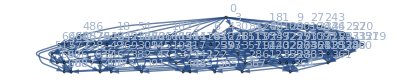

```mathematica
Graph[gCleaned,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->With[{g=allGraphs4[k,"graph"]},
Labeled[If[EdgeCount[g]==0,Framed[g],g],Style[k,Blue]]
],{k,fiveSorted}]]
```